```mathematica
OA1={{1.9882697947214076,34.76014760147601},
{2.8592375366568916,33.726937269372684}};
OA2={{2.8592375366568916,33.726937269372684},{
2.348973607038123,31.586715867158667}};
TA1={{2.348973607038123,31.586715867158667},{
3.736070381231672,29.815498154981544}};
TA2={{3.736070381231672,29.815498154981544},{
1.9882697947214076,22.50922509225092}};
SuperK={{1.9912023460410557,25.461254612546117},{
4.69208211143695,21.992619926199257}};
Stability={{1.9882697947214076,10.84870848708487},{
5.011730205278592,23.025830258302577}};
```

```mathematica
OA1plot=Plot[Interpolation[OA1,InterpolationOrder->1][x],{x,1,2.8592375366568916},PlotStyle->{Red,Dashed}];
OA2plot=Plot[Interpolation[OA2,InterpolationOrder->1][x],{x,2.348973607038123,2.8592375366568916},PlotStyle->{Red,Dashed}];
TA1plot=Plot[Interpolation[TA1,InterpolationOrder->1][x],{x,2.348973607038123,3.736070381231672},PlotStyle->{Red,Dashed}];
TA2plot=Plot[Interpolation[TA2,InterpolationOrder->1][x],{x,2.5,3.736070381231672},PlotStyle->{Red,Dashed}];
SuperKplot=Plot[Interpolation[SuperK,InterpolationOrder->1][x],{x,2.5,4.8},PlotStyle->{Red,Dashed}];
Stabilityplot=Plot[Interpolation[Stability,InterpolationOrder->1][x],{x,1,8},PlotStyle->{Black}];
canvasQball=Plot[-1,{x,2,7},PlotRange->{5,70},Frame->True,FrameStyle->Black,FrameLabel->{"m_S (GeV)","Q"}];
```

InterpolatingFunction::dmval: Input value {1.00004} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.00014} lies outside the range of data in the interpolating function. Extrapolation will be used.

#### Our constraints on Q ball

#### Explosiveness:

```mathematica
Qballboom[x_]:=38+4(x-3)
Qballflux[x_]:=60-4/3(x-3)
QballBH[x_]:=64-4(x-3)
boom=Plot[Qballboom[x],{x,2,8},PlotStyle->{Blue}];flux=Plot[Qballflux[x],{x,2,8},PlotStyle->{Red}];BH=Plot[QballBH[x],{x,2,8},PlotStyle->{Black}];
excluded=RegionPlot[{y≥Qballboom[x]&& y≤Min[Qballflux[x],QballBH[x]]},{x,1,8},{y,10,70}];
```

```mathematica
stability=RegionPlot[{0≤y≤ Interpolation[Stability,InterpolationOrder->1][x]},{x,1,7.5},{y,7,70},Mesh->Full];
```

InterpolatingFunction::dmval: Input value {1.00034} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.34211} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

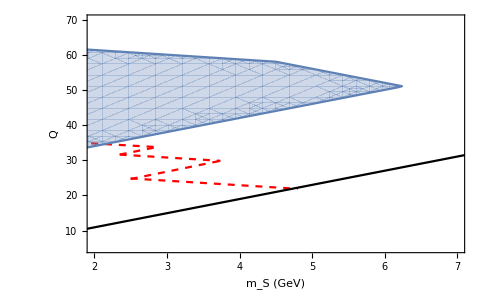

```mathematica
Show[canvasQball,OA1plot,OA2plot,TA1plot,TA2plot,SuperKplot,Stabilityplot,excluded]
```